# Supporting Information for Harnessing Matrix Completion to Unify and Extend Viral Serology Studies

The following code reproduces the plots in the main text. Made on Mathematica version 12.0.0 for Windows. Sections can be opened by mouse click.

Raw data can be found here.

## Figures

### Accessing the Data

#### Influenza (Fonville 2014)

The Fonville datasets are referred to by their SI table numbering: Table S1 (Fonville Study 1), Table S3 (Fonville Study 2), Table S5 (Fonville Study 3), Table S6 (Fonville Study 4), Table S13 (Fonville Study 5), and Table S14 (Fonville Study 6). For convenience, these table indices are stored in the variable:

```mathematica
(* List of all Fonville tables *)
fonvilleTables
```

{S1,S3,S5,S6,S13,S14}

For each dataset, the variables viruses and sera contain all the viruses and sera in that study. For example, here are the first five viruses and sera in Table S1

```mathematica
viruses["S1"][[;;5]]
sera["S1"][[;;5]]
```

{NL/179/93,A/WELLINGTON/1/94,A/BRISBANE/22/94,A/JOHANNESBURG/33/94,A/SHANGDONG/9/93}

{Serum_A/WELLINGTON/25/93_TableS1,Serum_A/WELLINGTON/96/93_TableS1,Serum_A/VICTORIA/9/94_TableS1,Serum_A/JOHANNESBURG/33/94_TableS1,Serum_A/SHANGDONG/9/93_TableS1}

For convenience, the table index All can be used to get a list of the viruses or sera in all Fonville studies

```mathematica
viruses[All]//Short
sera[All]//Short
```

{A/AUCKLAND/20/2003,A/AUCKLAND/5/96,A/BANGKOK/1/97,A/BEIJING/32/92,A/BRISBANE/10/2007,«71»,VN018/EL204/2009,VN019/EL442/2010,VN020/EL443/2010,VN021/EL444/2010,VN053/2010}

{Serum_A/WELLINGTON/25/93_TableS1,Serum_A/WELLINGTON/96/93_TableS1,Serum_A/VICTORIA/9/94_TableS1,«1141»,SubjectB025_TableS14_Post,SubjectB040_TableS14_Post,SubjectB039_TableS14_Post}

For each Fonville dataset, there are three types of data associated with it:

data: The raw data, with missing values represented by Missing[]

dataComplete: Intra-completed data, so that each virus-serum combination in that table has a value

dataAllComplete: Inter-completed data, where all six Fonville dataset were combined before completion

For example, the code below shows the raw measurements from Table S1 as well as the intra-completed measurements. Notice that the first output has Missing[] values while the second output does not.

```mathematica
(* Raw data *)
Table[data[{virus,serum}],{serum,sera["S1"]},{virus,viruses["S1"]}]
(* Intra-completed data *)
Table[dataComplete[{virus,serum}],{serum,sera["S1"]},{virus,viruses["S1"]}]
```

The intra-completed data (dataComplete) will not have virus-serum interactions if either the virus or serum do not exist in Table S1. However, the inter-completed data (dataAllComplete) will have these interactions. 
Note: It is difficult to estimate the uncertainty of these inter-table completion results. Based on the Figure 4B and Figure S5, such completions can have an RMSE anywhere from 0.2 to 1.2 for the log_10 titers.

```mathematica
(* Intra-completed data does not include viruses or sera outside of a table *)
dataComplete[{First@Complement[viruses[All],viruses["S1"]],First@sera["S1"]}]
(* Inter-completed data predicts all virus-serum interactions *)
dataAllComplete[{First@Complement[viruses[All],viruses["S1"]],First@sera["S1"]}]
```

dataComplete[{BI/16190/68,Serum_A/WELLINGTON/25/93_TableS1}]

16.526

#### HIV-1 (Catnap)

The HIV-1 data is accessible in a similar fashion to the influenza data, except that the table indices are either "Catnap" (for the monoclonal antibody data) or "CatnapPolyclonal" for the polyclonal serum data

```mathematica
(* Monoclonal antibody data *)
viruses["Catnap"]//Short
sera["Catnap"]//Short
```

{190049,191647,191859,191882,1245045,2833264,2969249,3514597,20721190,20803520,20915593,«912»,ZM214_15,ZM215_8,ZM233_6,ZM246F,ZM247_V1,ZM249_1,ZM53_12,ZM53_21,ZM55_28A,ZM55_4A}

{1357,1361,2158,2191,2219,2557,2558,2909,3019,3074,3694,3791,«349»,VRC-CH30,VRC-CH31,VRC-CH32,VRC-CH33,VRC-CH34,VRC-PG04,VRC-PG04b,VRC-PG05,VRC-PG19,VRC-PG20,Y498,Z13e1}

```mathematica
(* Polyclonal serum data *)
viruses["CatnapPolyclonal"]//Short
sera["CatnapPolyclonal"]//Short
```

{001428_2_42,00836_2_5,16055_2_3,16936_2_21,246_F3_C10_2,25710_2_43,25711_2_4,25925_2_22,«55»,ZM109_32,ZM109_4,ZM135_10A,ZM197_7,ZM214_15,ZM233_6,ZM249_1,ZM53_12}

{Polyclonal AIIMS_329 102-months,Polyclonal AIIMS_329 112-months,Polyclonal AIIMS_329 117-months,«34»,polyclonal Patient 8,polyclonal PC64-M35,polyclonal QA013}

For each dataset, there are two types of data associated with it:

data: The raw data, with missing values represented by Missing[]

dataComplete: The matrix-completed dataset, where each virus-serum combination has a value

Because these two dataset have different units, we did not combine them and create a dataAllComplete variable for Catnap

For example, the code below provides the raw measurements for the monoclonal antibody dataset as well as the matrix-completed data.

```mathematica
(* Raw data *)
Table[data[{virus,serum}],{serum,sera["Catnap"]},{virus,viruses["Catnap"]}]
(* Intra-completed data *)
Table[dataComplete[{virus,serum}],{serum,sera["Catnap"]},{virus,viruses["Catnap"]}]
```

### Methods of Matrix Completion

In this manuscript, we performed matrix completion using nuclear norm minimization. This method is implemented via the function nuclearNormMinimization. Given a matrix M with missing values (denoted by the Head Missing), this method searches for a complete matrix M̃ found by the optimization algorithm

minimize | (‖M̃‖)_*
subject to | ((M̃)_measured)_(j,k)=(M_measured)_(j,k)

M_measured represents the non-missing values in M, so that M̃ must exactly match M at these measured values, and the missing values are filled in by minimizing the nuclear norm of the resulting matrix. The nuclear norm (or trace norm) is equal to (‖M̃‖)_*=Tr[((M̃)^*M̃)^(1/2)] where (M̃)^* denotes the conjugate transpose of M̃.

In this notebook, we use a related algorithm called robust PCA that scales better for larger matrices. This method is implemented with the function RPCA and solves the same minimization problem. The differences between both algorithms tend to be very minor - for example, the section below shows that for a Fonville dataset, both approaches yield the same result, although robust PCA is significantly faster for larger datasets.

Note that for both nuclear norm minimization and robust PCA, we force an exact match for the measured values in the completed matrix, whereas in our manuscript we enabled the measured values to deviated with a quadratic penalty. As shown in Table S1, the RMSE of the measured values was ≤0.06 for the log_10 data across all matrices (corresponding to 10^0.06=1.15-fold error), so that enforcing this exact match will minimally alter the results.

#### Basic Examples of Matrix Completion

Consider the following complete rank 1 matrix.

```mathematica
matrixComplete=# Range@5&/@ Range@5;
Echo[matrixComplete//MatrixForm,"Complete matrix: "];
```

Complete matrix:  (1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25)

Remove 4 entries and matrix complete using the nuclear norm and robust PCA algorithms. In this example, nuclear norm minimization leads to nearly perfect completion, while robust PCA has slightly larger error.

```mathematica
matrixIncomplete=matrixComplete;
(matrixIncomplete[[Sequence@@#]]=Missing[])&/@{{1,2},{3,4},{5,1},{2,4}};
Echo[(matrixIncomplete//MatrixForm)->(Round[nuclearNormMinimization[matrixIncomplete],0.01]//MatrixForm),"Nuclear norm matrix completion:"];
Echo[(matrixIncomplete//MatrixForm)->(Round[RPCA[matrixIncomplete],0.01]//MatrixForm),"Robust PCA matrix completion:"];
```

Nuclear norm matrix completion: (1 | Missing[] | 3 | 4 | 5
2 | 4 | 6 | Missing[] | 10
3 | 6 | 9 | Missing[] | 15
4 | 8 | 12 | 16 | 20
Missing[] | 10 | 15 | 20 | 25)→(1. | 2. | 3. | 4. | 5.
2. | 4. | 6. | 7.99 | 10.
3. | 6. | 9. | 12. | 15.
4. | 8. | 12. | 16. | 20.
5. | 10. | 15. | 20. | 25.)

Robust PCA matrix completion: (1 | Missing[] | 3 | 4 | 5
2 | 4 | 6 | Missing[] | 10
3 | 6 | 9 | Missing[] | 15
4 | 8 | 12 | 16 | 20
Missing[] | 10 | 15 | 20 | 25)→(1. | 2.36 | 3. | 4. | 5.
2. | 4. | 6. | 7.61 | 10.
3. | 6. | 9. | 11.44 | 15.
4. | 8. | 12. | 16. | 20.
4.32 | 10. | 15. | 20. | 25.)

Both matrix completion algorithms perform nearly identically on the datasets considered in this study. For example, when removing 50% of the data in Fonville 2014 Study 1 (Table S1) and performing matrix completion, the predictions for all 50% of values are shown below - nearly every large blue point (nuclear norm minimization) has a small gold point (robust PCA) that lies directly on top, and the RMSE of these predictions are the same up to the hundredths decimal point.

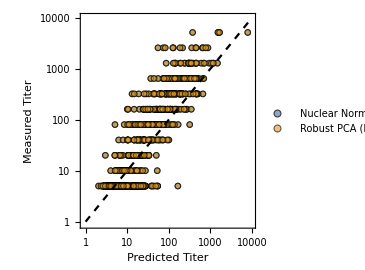

```mathematica
posWithheld=;
(* Fonville Study 1 with 50% of values withheld *)
matrixComplete=Table[data[{virus,serum}],{serum,sera["S1"]},{virus,viruses["S1"]}]/.Missing[]->Missing["Not Measured"];
matrixIncomplete=ReplacePart[matrixComplete,posWithheld->Missing["Withheld"]];
(* Matrix complete - The LogData option performs completion on the Subscript[Log, 10] titers *)
resRPCA=RPCA[matrixIncomplete,"LogData"->True];
plotDataRPCA=Transpose[Extract[#,posWithheld]&/@{resRPCA,matrixComplete}];
resNucNorm=nuclearNormMinimization[matrixIncomplete,"LogData"->True];
plotDataNucNorm=Transpose[Extract[#,posWithheld]&/@{resRPCA,matrixComplete}];
(* Plotting *)
Show[ListPlot[{plotDataRPCA,plotDataNucNorm},PlotRange->ConstantArray[{0.9,10^4},2],ScalingFunctions->{"Log","Log"},ImageSize->270,PlotMarkers->{plotMarker[0.04,0.7],plotMarker[0.02,0.6]},AspectRatio->1,Frame->{True,True,False,False},FrameTicks->ConstantArray[LogTicks[10^0,10^3.2,TickLengthScale->3],2],FrameStyle->Thickness[0.003],FrameLabel->(font/@{"Predicted Titer","Measured Titer"}),PlotLegends->PointLegend[{Row[{"Nuclear Norm (RMSE=",Round[RootMeanSquare[Subtract@@@Log10@N@plotDataNucNorm],0.01],")"}],Row[{"Robust PCA (RMSE=",Round[RootMeanSquare[Subtract@@@Log10@N@plotDataRPCA],0.01],")"}]},LegendFunction->"Frame"]],Plot[{x},{x,1,10^4},PlotStyle->{Black,Thick,Dashed},ScalingFunctions->{"Log","Log"}]]
```

The primary advantage of robust PCA is that it scales better with the size of the matrix. For example, for Fonville Study 3 (Table S5), robust PCA is 10-fold faster than nuclear norm minimization

```mathematica
matrixIncomplete=Table[data[{virus,serum}],{serum,sera["S5"]},{virus,viruses["S5"]}];
Echo[First@Timing@RPCA[matrixIncomplete,"LogData"->True],"Timing for Robust PCA (seconds):"];
Echo[First@Timing@nuclearNormMinimization[matrixIncomplete,"LogData"->True],"Timing for Robust PCA (seconds):"];
```

Timing for Robust PCA (seconds): 1.59375

Timing for Robust PCA (seconds): 17.8906

### Figure 2: Influenza Intra-Table Completion (Fonville 2014)

Analysis of the influenza data in Fonville 2014. Panel A shows the intra-table completion process, where missing and withheld entries are filled in via matrix completion. Panel B shows the accuracy of imputing the withheld values. Panel C shows the approximate rank of the resulting complete matrix. All three panels correspond to a single matrix completion run for Fonville Table S1 with 50% of data observed.

In Panel D, we vary the fraction of data observed across all Fonville tables and analyze how the r^2 and the RMSE improve as more values are seen. For reference, the error of the experimental assay is approximately 2-fold, corresponding to Log_10[2]≈0.3 on the RMSE plot.

#### Panels A-C: 1 Run at 50% Observed Fraction

```mathematica
(* Fonville Study 1 with 50% of values withheld *)
posWithheld=;
dataMeasurements=Table[data[{virus,serum}],{serum,sera["S1"]},{virus,viruses["S1"]}]/.Missing[]->Missing["Not Measured"];
dataPreCompletion=ReplacePart[dataMeasurements,posWithheld->Missing["Withheld"]];
(* Matrix complete - The option specifies that the Log10[titers] are completed *)
dataPostCompletion=RPCA[dataPreCompletion,"LogData"->True];
```

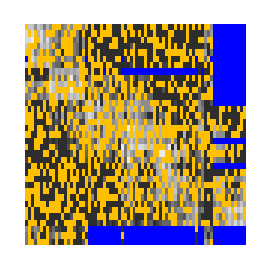
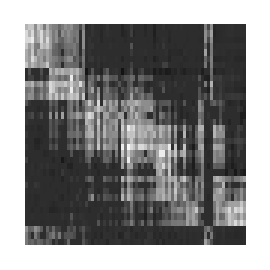
-Graphics- | -Graphics-
 |

```mathematica
(* Panel A *)
leg1=SwatchLegend[{colorMissing,colorWithheld},font/@{"Missing","Validation"},LegendFunction->"Frame"];
leg2=BarLegend[{GrayLevel,{0,4}},LegendLayout->"Row",LegendLabel->font["Titer",14],Ticks->Table[{j,Superscript[10,j]},{j,0,4}]];
{plotArrayPreCompletion,plotArrayPostCompletion}=ArrayPlot[N@#/.val_Real:>Log10@val,PlotRangePadding->None,ColorFunction->(Which[MatchQ[#,_Real],GrayLevel[Rescale[#,{0,4}]],MemberQ[#,Missing["Withheld"],All],colorWithheld,MemberQ[#,Missing["Not Measured"],All],colorMissing]&),ColorFunctionScaling->False,AspectRatio->1,ImageSize->270]&/@{dataPreCompletion,dataPostCompletion};
Grid[{{plotArrayPreCompletion,plotArrayPostCompletion},{leg1,leg2}},Spacings->{3,1}]
```

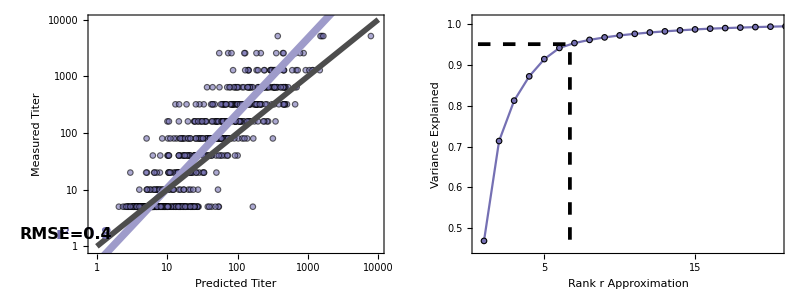

```mathematica
(* Panel B *)
plotData=Transpose[Extract[#,posWithheld]&/@{dataPostCompletion,dataMeasurements}];
fit=fitPerp[Log10@plotData];
fit=10^(fit/.x->Log10[x]);
plotScatter=Show[ListPlot[plotData,],Plot[{fit,x},{x,1,10^4},]];
(* Panel C *)
σVals=SingularValueList[Log10@dataPostCompletion-Mean@Flatten@Log10@dataPostCompletion];
plotData=Transpose[{Range@Length@σVals,Accumulate[σVals^2]/Total[σVals^2]}];
f=Interpolation[plotData];
root=x/.FindRoot[f[x]==0.95,{x,7.}];
plotRank=ListPlot[plotData,];
Grid[{{plotScatter,plotRank}},Spacings->3]
```

#### Panel D: r^2 and RMSE at Different Observed Fractions

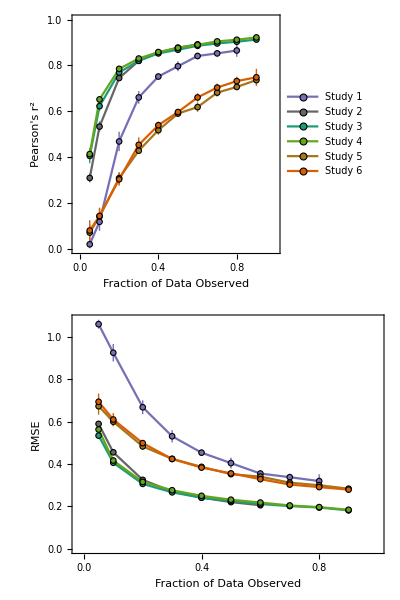

```mathematica
Block[{canned={,}},
leg=PointLegend[colors,font["Study "<>ToString@#]&/@Range@6,];
plots=MapIndexed[(
plotData=canned[[First@#2]];
Show[ListPlot[plotData,]]
)&,{{{2,3},"Pearson's r^2",{0,1.}},{{2,4},"RMSE",{0,1.08}}}];
Grid[{{plots[[1]]},{plots[[2]]}},Spacings->2]
]
```

### Figure 3: HIV-1 Intra-Table Completion (Catnap)

Analysis of the HIV-1 data from Catnap (a collection of multiple large-scale serological studies).The format of this figure parallels that of Figure 2.

#### Panels A-C: 1 Run at 50% Observed Fraction

For numerical stability, we always set the strongest antibody-virus interactions as the largest values. Therefore, we set up the matrix completion for the Catnap monoclonal antibody data using -Log_10[IC_50 values]. (In contrast, the polyclonal serum data and the Fonville serum data are all matrix completed as -Log_10[titers].)

```mathematica
(* Catnap monoclonal antibody data with 13% of values withheld *)
posWithheld=;
dataMeasurements=Table[data[{virus,serum}],{serum,sera["Catnap"]},{virus,viruses["Catnap"]}]/.Missing[]->Missing["Not Measured"];
dataPreCompletion=ReplacePart[dataMeasurements,posWithheld->Missing["Withheld"]];
(* Matrix complete - The option specifies that the -Log10[titers] are completed *)
(* This completion takes a while because the Catnap dataset is significantly larger than the Fonville datasets *)
dataPostCompletion=RPCA[dataPreCompletion,1000,"LogData"->True,"InvertData"->True];
```

```mathematica
(* Panel A *)
(* For better visibility, show each withheld value as a 2x6 gold square *)
posWithheldExtra=DeleteCases[Flatten[Table[pos+{x,y},{pos,posWithheld},{x,-1,1},{y,-3,3}],2],{0|(1+First@Dimensions@dataPreCompletion),_}|{_,0|(1+Last@Dimensions@dataPreCompletion)}];
(* Pre- and post-completion matrix *)
range={-5.2,4.1};
{plotArrayPreCompletion,plotArrayPostCompletion}=ArrayPlot[N@#/.val_Real:>Log10@val,PlotRangePadding->None,ColorFunction->(Which[MatchQ[#,_Real],GrayLevel[1-Rescale[#,range]],MemberQ[#,Missing["Withheld"],All],colorWithheld,MemberQ[#,Missing["Not Measured"],All],colorMissing]&),ColorFunctionScaling->False,AspectRatio->1,ImageSize->270]&/@{ReplacePart[dataPreCompletion,posWithheldExtra->Missing["Withheld"]],dataPostCompletion};
(* Plotting *)
leg1=SwatchLegend[{colorMissing,colorWithheld},font/@{"Missing","Validation"},LegendFunction->"Frame"];
leg2=BarLegend[{GrayLevel[1-Rescale[#,range]]&,range},LegendLayout->"Row",LegendLabel->font["IC_50 (μg/mL)",14],Ticks->Table[{j,Superscript[10,j]},{j,-4,4,2}]];
Grid[{{plotArrayPreCompletion,plotArrayPostCompletion},{leg1,leg2}},Spacings->{3,1}]
```

-Graphics- | -Graphics-
 |

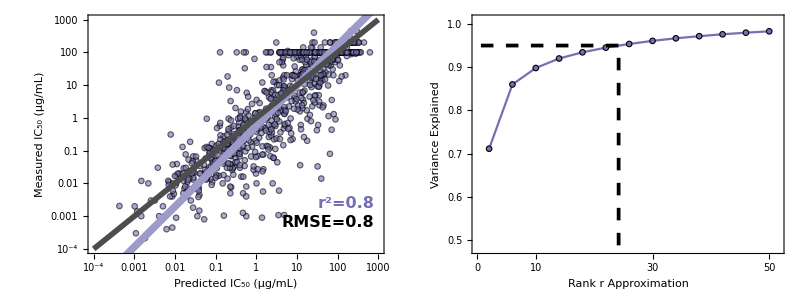

```mathematica
(* Panel B *)
plotData=Transpose[Extract[#,posWithheld]&/@{dataPostCompletion,dataMeasurements}];
fit=fitPerp[Log10@N@plotData];
fit=10^(fit/.x->Log10[x]);
plotScatter=Show[ListPlot[plotData,],Plot[{fit,x},{x,10^-4,10^3},]];
(* Panel C *)
σVals=SingularValueList[Log10@dataPostCompletion-Mean@Flatten@Log10@dataPostCompletion];
plotData=Transpose[{Range@Length@σVals,Accumulate[σVals^2]/Total[σVals^2]}][[2;;50;;4]];
f=Interpolation[plotData];
root=x/.FindRoot[f[x]==0.95,{x,7.}];
plotRank=ListPlot[plotData,];
Grid[{{plotScatter,plotRank}},Spacings->3]
```

#### Panel D: r^2 and RMSE at Different Observed Fractions

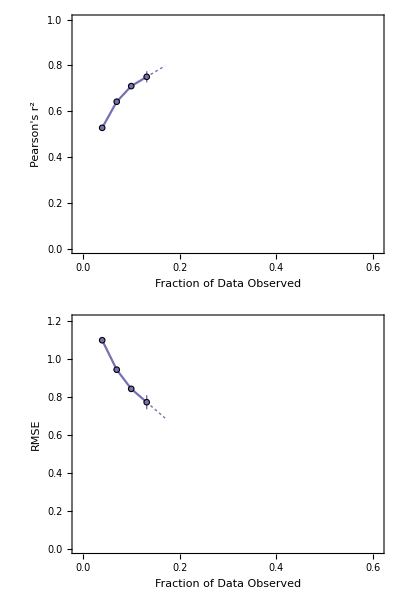

```mathematica
Block[{canned={,}},
plots=MapIndexed[(
plotData=resIntraCatnapAnalysis[[All,#[[1]]]];
fit=Fit[{#[[1]],#[[2]]["Value"]}&/@plotData[[-2;;]],{1,x},x];
Show[ListPlot[plotData,],Plot[fit,{x,0.14,0.17},]]
)&,{{{1,2},"Pearson's r^2",{0,1}},{{1,3},"RMSE",{0,1.21}}}];
Grid[{{plots[[1]]},{plots[[2]]}},Spacings->2]
]
```

### Figure 4: Inter-Table Completion

Panel B examines how well a virus can be inter-table completed between two Fonville tables. For example, suppose a virus V is present in Tables S1, S5, and S6. We perform three different matrix completions, withholding all virus V data from one of the tables, performing matrix completion, and comparing the imputed values to the measured values.

Panel C demonstrates inter-table completion across the Catnap monoclonal antibody IC_50 data and the polyclonal serum ID_50 data. Although straightforward matrix completion between the two datasets leads to large error (6–10-fold), the results nevertheless allow us to accurately characterize which of the missing antibodies/sera have the strongest interactions with a virus. Said another way, given that the monoclonal antibody data spans 6 orders of magnitude, 10-fold error is more than sufficient to differentiate between the strongest and weakest interactions.

#### Panel B: Completion across Fonville Studies

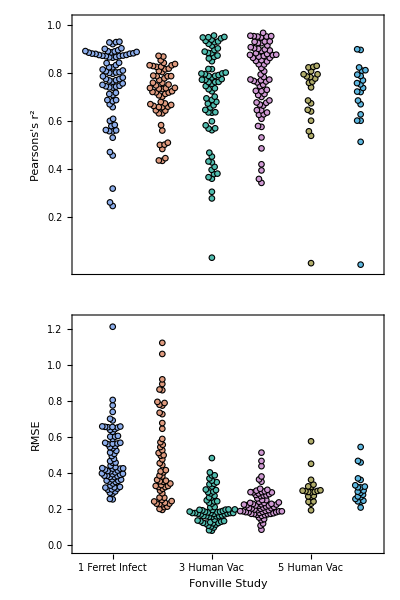

```mathematica
resInterAnalysis=;
(* Cases where the standard deviation of the either the predicted or measured titers is <0.2, which artificially deflates r^2 *)
lowStandardDeviation=Cases[listInter,entry_/;(Min[StandardDeviation/@Transpose@N@Log10[resInter@entry]]<0.2)];
(* Swarm plots *)
{plotCorrelation,plotRMSE}=With[{r=0.012,plotRangeX={0.3,6.35}},
Switch[#,
"Pearsons's r^2",
index=-2;
frameTicks={{LinTicks[0,1.25,TickLengthScale->2]/."0.0"->"",None},{LinTicks[1,6,TickLengthScale->2,TickLabelStart->2,ShowMinorTicks->False],None}};
plotRange={plotRangeX,{-0.02,1.02}},
"RMSE",
index=-1;
frameTicks={{LinTicks[0,1.25,TickLengthScale->2],None},{MapIndexed[{First@#2,Column[font/@Prepend[#,First@#2],Alignment->Center,Spacings->0],{0.02,0}}&,{{"Ferret","Infect"},{"Human","Infect"},{"Human","Vac"},{"Human","Vac"},{"Human","Vac"},{"Human","Vac"}}](*{{1.,"1",{0.02,0},{}},{2.,"2",{0.02,0},{}},{3.,"3",{0.02,0},{}},{4.,"4",{0.02,0},{}},{5.,"5",{0.02,0},{}},{6.,"6",{0.02,0},{}}}*),None}};
plotRange={plotRangeX,{-0.02,1.25}}
];
coords=MapIndexed[swarm[Sort@DeleteCases[Cases[resInterAnalysis,{{_,#},__}],entry_/;If[index==-2,(* Remove cases with artifically deflated r^2 *)MemberQ[lowStandardDeviation,First@entry],{}]][[All,index]],2r,First@#2,Divide@@Subtract@@@plotRange]&,fonvilleTables];
ListPlot[coords,Frame->True,PlotRange->plotRange,ImageSize->270,PlotStyle->ColorData[95],PlotMarkers->plotMarker[0.95 2r],FrameTicks->frameTicks,FrameStyle->Thickness[0.0015],FrameLabel->(If[#=="RMSE",font[#,16]&/@{"Fonville Study",#},font[#,16]]),FrameTicksStyle->Directive[14,colorTicks]]
]&/@{"Pearsons's r^2","RMSE"};
Grid[{{plotCorrelation},{plotRMSE}}]
```

#### Panel C: Completion between Catnap Monoclonal and Polyclonal Data

Since the monoclonal and polyclonal Catnap dataset have different units, before matrix completion they were both separately mean-centered (as specified by the variables $shiftMonoclonal and $shiftPolyclonal), and the monoclonal data was inverted (so that the strongest antibody-virus interactions are denoted by the largest values). Thus, we recover the un-logged IC_50 values for the monoclonal antibody data using $shiftMonoclonal 10^-IC50 and recover the un-logged ID_50 values for the polyclonal serum data using $shiftPolyclonal 10^-ID50.

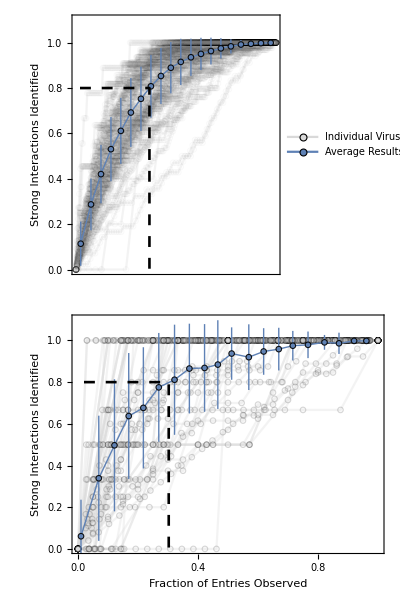

```mathematica
(* Analyze all viruses within either the 'withheldData'="Monoclonal" or 'withheldData'="Polyclonal" datasets *)
plotCatnapInter[withheldData_]:=Block[{Δx=0.05,threshold=0.8,cannedMonoclonal=,cannedPolyclonal=},
(* Responses of the individual viruses *)
individualResponses=DeleteMissing[If[withheldData==="Monoclonal",cannedMonoclonal,cannedPolyclonal]];
(* Mean response across all viruses, using a window of Δx *)
meanResponse=Join@@individualResponses;
meanResponseAvg=Table[{Mean[First/@#],Around[Mean[Last/@#],StandardDeviation[Last/@#]]}&@Cases[meanResponse,{x_,_}/;xMin≤x<xMin+Δx],{xMin,0,1-Δx,Δx}];
(* Demark when 80% of the key interactions are found *)
f=Interpolation[meanResponseAvg/.Around[mean_,_]:>mean];
root=x/.FindRoot[f[x]-threshold,{x,0.3}];
Show[ListPlot[individualResponses,],ListPlot[meanResponseAvg,]]
]
Grid[{{plotCatnapInter["Monoclonal"]},{plotCatnapInter["Polyclonal"]}},Spacings->3]
```

### Figure 5: Prioritizing Monoclonal Antibody Measurements

Using existing Catnap measurements up to a certain year to predict future measurements. In the plot below, we use predict all virus-antibody IC_50 values from 2018 and later. We sort the imputed IC_50 values from strongest-to-weakest and examined how many strong interactions (IC_50<0.1 μg/mL) are identified by N experiments (x-axis). In Figure S7, we show how potent or weak interactions could be predicted across several years.

```mathematica
predictFutureExperiments[2018,"PotentInteractions"]
```

-Graphics-

### Figure S2: Antigenic Clustering of Fonville Data

We compare the inhibition profiles of each virus with their antigenic cluster defined via cartography (see Figure 1 of Fonville 2014). While there is similarity between both approaches, there are several cases where viruses in different clusters have more similar inhibition profiles than viruses in the same antigenic cluster.

```mathematica
(* Antigenic clusters from Fonville 2014 Figure S1 *)
fonvilleClusters=;
numClusters=Max[Last/@fonvilleClusters];
colorClusters=Thread[Range@numClusters->Reverse[ColorData["Rainbow"]/@Subdivide[numClusters-1]]];
```

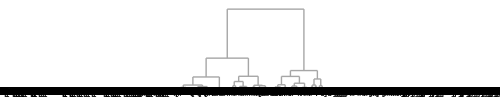
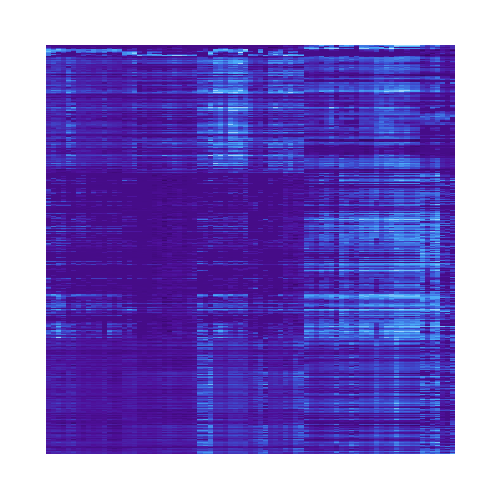
-Graphics- | 



-Graphics- |

```mathematica
imageSize=500;
plotData=Log10@Table[dataAllComplete[{virus,serum}],{serum,sera[All]},{virus,viruses[All]}];
res=Dendrogram[Transpose@plotData->(viruses[All]),ClusterDissimilarityFunction->"Ward",PlotRangePadding->None,ImageSize->imageSize,AspectRatio->1/5];
plotDataSorted=Log10@Table[dataAllComplete[{virus,serum}],{serum,sera[All]},{virus,res[[1,2;;,1,1,1]]}];
(* Plotting *)
leg1=SwatchLegend[Last/@colorClusters,First/@colorClusters,LegendLayout->{"Column",1},LegendLabel->Placed[Column[font[#,14]&/@{"Antigenic","Cluster"},Alignment->Center],Above],LegendFunction->"Frame"];
leg2=BarLegend[{"DeepSeaColors",MinMax@plotData},LegendLayout->"Column",LegendLabel->font["Titer",14],Ticks->Table[{j,Superscript[10,j]},{j,0,4}]];
grid=Grid[{{res/.(fonvilleClusters/.colorClusters),Column[{leg1,leg2,"",""},Spacings->3]},{ArrayPlot[plotDataSorted,ImageSize->imageSize,AspectRatio->1,PlotRangePadding->None,ColorFunction->"DeepSeaColors",FrameTicks->{None,MapIndexed[{First@#2,Rotate[font[#1,6],π/2]}&,res[[1,2;;,1,1,1]]],None,None}(*,FrameLabel->{None,font["Viruses",14]}*)],SpanFromAbove}},Alignment->{Center,Center}]
```

### Figure S3: Fonville Inter-Table Completion (Individual Virus Results)

We show the results for each individual virus-table combination for the Fonville inter-table completions in Figure 4B.

```mathematica
(* {Virus left out, table removed from, # tables containing virus, correlation, RMSE, my R^2} *)
resInterAnalysis=;
(* Cases where the standard deviation of the either the predicted or measured titers is <0.2, which artificially deflates r^2 *)
lowStandardDeviation=;
```

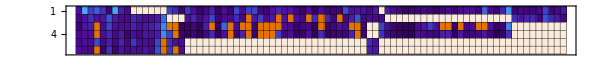
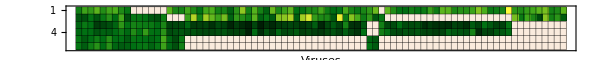
-Graphics- |   
-Graphics- |

```mathematica
(* Sort the viruses based on how many tables they are in *)
virusesSorted=ReverseSortBy[viruses[All],containingTables];
(* Min/Max values of RMSE and r^2 *)
{arrayCorrelation,arrayRMSE}=ArrayPlot[
Switch[#,
"Correlation",
index=-2;
colorTheme="DeepSeaColors";
bounds={1.0,0},

"RMSE",
index=-1;
colorTheme="AvocadoColors";
bounds={0,1.2}
];
Table[
res=If[#=="Correlation"&&MemberQ[lowStandardDeviation,{virus,table}],Missing["Low Standard Deviation"],FirstCase[resInterAnalysis,{{virus,table},__}]];

If[MissingQ@res,res,res[[index]]]
,{table,fonvilleTables},{virus,virusesSorted}],ColorFunction->(ColorData[colorTheme][Rescale[#,bounds]]&),PlotLabel->font[#/.{"Correlation"->"Pearson's r^2"},18],Frame->True,FrameLabel->{None,If[#=="RMSE",font["Viruses",14],None]},FrameTicks->{Range@6,None},ColorFunctionScaling->False,ColorRules->{Missing["Low Standard Deviation"]->Darker[Orange,0.1],Missing["NotFound"]->RGBColor[0.9804104442683171, 0.9215859029086462, 0.8666837120812164]},Mesh->True,MeshStyle->Directive[Thickness[0.0005],Black],ImageSize->600,AspectRatio->0.1,PlotRangePadding->None]&/@{"Correlation","RMSE"};
Block[{opts={LabelStyle->Directive[FontSize->16],FrameStyle->Directive[Black,Thickness[Small]],Charting`TicksStyle->Directive[FontColor->colorTicks,Thickness[Medium]],LegendMarkerSize->100}},
legArrayCorrelation=BarLegend[{ColorData["DeepSeaColors"][1-#]&,{0,1}},Ticks->Table[j,{j,0,1,0.5}],Evaluate@opts];
legArrayRMSE=BarLegend[{"AvocadoColors",{0,1.2}},Ticks->Table[j,{j,0,1.2,0.4}],Evaluate@opts];
legSwatchCorrelation=SwatchLegend[{RGBColor[0.9804100067361553, 0.9215680276794109, 0.8666658310700697],RGBColor[0.9017317961412896, 0.45073363470217104, 1.9375701157334225*^-6]},font[#,14]&/@{"Not in Study","Low Standard Deviation"},LegendFunction->"Frame"];
legSwatchRMSE=SwatchLegend[{RGBColor[0.9804100067361553, 0.9215680276794109, 0.8666658310700697]},font[#,14]&/@{"Not in Study"},LegendFunction->"Frame"];

Grid[{{arrayCorrelation,Row[{legArrayCorrelation,"  ",legSwatchCorrelation}]},{arrayRMSE,Row[{legArrayRMSE,"  ",legSwatchRMSE}]}},Spacings->3,Alignment->{Left,Top}(*Top*)]
]
```

### Figure S4: Inter-Table Completion with Multiple Viruses Left Out

Inter-table completion, where a single virus is entirely removed from a dataset and imputed via matrix completion, works remarkably well for Fonville Tables S5/S6 and S13/S14 (Studies 3/4 and 5/6). This figure explores how well multiple viruses can be withheld from a dataset and imputed via matrix completion.

For simplicity, we either use Table S5 to predict values in Table S6 (denoted by Table S5→Table S6 in the figure) or use Table S13 to predict values in Table S14 (denoted by Table S13→Table S14), without looking at the reverse directions.

The rationale behind this choice is that the measurements in Tables S5 and S6 were carried out in 1997 and 1998, respectively, so that measurements in Table S6 could have been informed by the measurements carried out a year earlier for Table S5. Similarly, Tables S13 and S14 were carried out in 2009 and 2010, respectively.

#### Example Matrix Completion

```mathematica
(* Choose which set of viruses to withhold *)
Clear[virusesToWithhold]
virusesToWithhold[table_,stepSize_:4,numReplicates_:10]:=(
SeedRandom[12345];
Join@@Table[{#,table}&/@RandomSample[viruses[table],numVirusesToWithhold]
,{numVirusesToWithhold,Range[1,Length@viruses[table]-1,stepSize]},{replicate,numReplicates}]
)
```

```mathematica
(* Example: Withhold 5 viruses from Table S6 *)
listWithheld=virusesToWithhold["S6"][[20]]
```

{{A/JOHANNESBURG/33/94,S6},{A/PHILIPPINES/427/2002_MDCK,S6},{A/VICTORIA/1/93,S6},{A/SOUTH_AUSTRALIA/53/2001,S6},{A/URUGUAY/716/2007,S6}}

```mathematica
(* Incomplete matrix with withheld values *)
matrixIncomplete=matrixComplete=generateDataLeaveOneOut[listWithheld,All];
(* Matrix completion *)
matrixComplete[[2;;,2;;]]=RPCA[matrixIncomplete[[2;;,2;;]],200,"LogData"->True];
(* RMSE for all withheld values *)
RootMeanSquare[Subtract@@@Log10@N[Join@@(DeleteMissing[extractCompletionPredictions[matrixComplete,#,data],1,All]&/@listWithheld)]]
```

0.219354

#### Calculating all Matrix Completions

Withhold multiple viruses from Table S6

```mathematica
(* Choose which set of viruses to withhold *)
Clear[virusesToWithhold]
virusesToWithhold[table_,stepSize_:4,numReplicates_:10]:=(
SeedRandom[12345];
Join@@Table[{#,table}&/@RandomSample[viruses[table],numVirusesToWithhold]
,{numVirusesToWithhold,Range[1,Length@viruses[table]-1,stepSize]},{replicate,numReplicates}]
)
```

```mathematica
resWithholdMultiS6=Table[
(* Incomplete matrix with withheld values *)
matrixIncomplete=matrixComplete=generateDataLeaveOneOut[listWithheld,All];
(* Matrix completion *)
matrixComplete[[2;;,2;;]]=RPCA[matrixIncomplete[[2;;,2;;]],200,"LogData"->True];
(* RMSE for all withheld values *)
listWithheld->RootMeanSquare[Subtract@@@Log10@N[Join@@(DeleteMissing[extractCompletionPredictions[matrixComplete,#,data],1,All]&/@listWithheld)]]
,{listWithheld,virusesToWithhold["S6"]}]
```

```mathematica
resWithholdMultiS14=Table[
(* Incomplete matrix with withheld values *)
matrixIncomplete=matrixComplete=generateDataLeaveOneOut[listWithheld,All];
(* Matrix completion *)
matrixComplete[[2;;,2;;]]=RPCA[matrixIncomplete[[2;;,2;;]],200,"LogData"->True];
(* RMSE for all withheld values *)
listWithheld->RootMeanSquare[Subtract@@@Log10@N[Join@@(DeleteMissing[extractCompletionPredictions[matrixComplete,#,data],1,All]&/@listWithheld)]]
,{listWithheld,virusesToWithhold["S14",2]}]
```

#### Figure

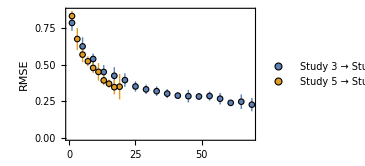

```mathematica
(* Canned results *)
resWithholdMulti["S6"]=;
resWithholdMulti["S14"]=;
(* Plotting *)
plotData=Table[{Length@viruses[table]-Length@#[[1,1]],Around[Mean[Last/@#],StandardDeviation[Last/@#]]}&/@SplitBy[resWithholdMulti[table],Length@First@#&],{table,{"S6","S14"}}];
ListPlot[plotData,]
```

### Figure S5: Fonville Inter-Table Completions using a Subset of Studies

Rather than using the combination of all Fonville tables when performing the inter-table completion, we restrict the completion to only use a subset of tables. In this way, we can determine how well matrix completion works across different types of data (i.e. ferret vs human or vaccination vs infection).

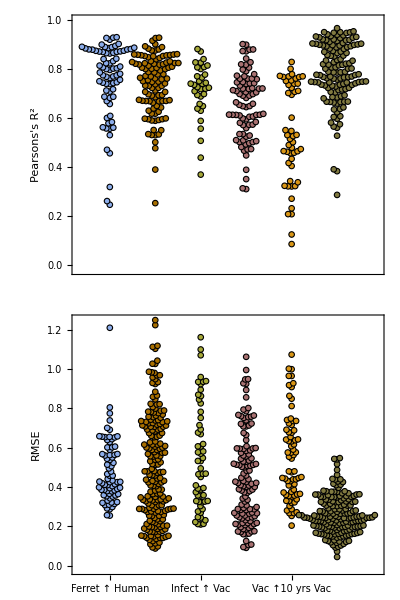

```mathematica
(* Swarm plots *)
Block[{cannedRSquared=,cannedRMSE=},
{plotRSquared,plotRMSE}=With[{r=0.012},
plotRange={{0.3,6.9},{-0.02,If[#==="RSquared",1.,1.25]}};
coords=MapIndexed[swarm[Sort@#,2r,First@#2,Divide@@Subtract@@@plotRange]&,If[#==="RSquared",cannedRSquared,cannedRMSE]];
ListPlot[coords,Frame->True,PlotRange->plotRange,ImageSize->270,PlotStyle->Prepend[ColorData[72]/@Range[2,6],ColorData[95][1]],PlotMarkers->plotMarker[0.95 2r],FrameTicks->{{LinTicks[0,1.25,TickLengthScale->2],None},{If[#=="RSquared",LinTicks[1,6,TickLengthScale->2,TickLabelStart->2,ShowMinorTicks->False],MapIndexed[{First@#2,Column[font/@#,Alignment->Center,Spacings->0],{0.02,0}}&,{{"Ferret","↑","Human"},{"Human","↑","Ferret"},{"Infect","↑","Vac"},{"Vac","↑","Infect"},{"Vac",Row[{"     ↑",font["10 yrs",8,Gray]}],"Vac"},{"Vac",Row[{"    ↑",font["1 yr",8,Gray]}],"Vac"}}]],None}},FrameLabel->font[#/."RSquared"->"Pearsons's R^2",14],FrameStyle->Thickness[0.0015],FrameTicksStyle->Directive[14,colorTicks]]
]&/@{"RSquared","RMSE"};
Grid[{{plotRSquared},{plotRMSE}}]
]
```

### Figure S6: Accuracy of Matrix Completion vs Virus Divergence

Here, we probe how the accuracy of intra-table completion matrix completion depends upon the similarity of the viruses in the dataset.

For each virus V, we choose n other viruses whose amino acid Hamming distance (ΔAA) is greater than some threshold value (x-axis in the figure). n=9 for the influenza data and n=34 for the HIV-1 data. These values are large enough to permit accurate matrix completion but small enough to probe the full range of virus dissimilarity seen in each dataset.

For influenza, we only focus on viruses in Fonville Table S6 (chosen because it has nearly-complete data and a large virus panel). For HIV-1, we use the Catnap data

```mathematica
resFonvilleLargeAA=;
resCatnap=;
```

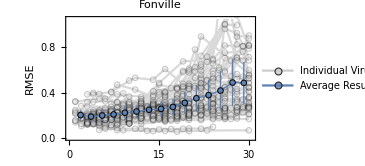

```mathematica
plotData=DeleteCases[resFonvilleLargeAA,{x_,y_}/;x>30,{2}];
mean={N@Mean[First/@#],If[Length@#==1,First@#,Around[Mean[#],StandardDeviation[#]]]&[Last/@#]}&/@GatherBy[Sort[Join@@Values@plotData],Floor[First[#],2]&];
(*mean=Cases[mean,{x_,y_}/;100<x<200];*)
leg=LineLegend[Directive[Thick,#]&/@{GrayLevel[0.8],ColorData[97][1]},font[#,14]&/@{"Individual Virus","Average Results"},LegendMarkers->plotMarker[0.04,0.8],LegendFunction->frameOpaque,Spacings->{0.2,0.4}];
plotFonville=Show[ListPlot[plotData,AxesOrigin->{0,0},Frame->{True,True,False,False},PlotLabel->font["Fonville",18],FrameLabel->(font[#,16]&/@{"ΔAA to Nearest Virus","RMSE"}),PlotMarkers->plotMarker[0.025,0.2],PlotRange->{{0,30.5},{Automatic,1.05}},Joined->True,PlotStyle->LightGray,PlotLegends->Placed[leg,Scaled[{{0.33,0.805},{0.5,0.5}}]],ImageSize->270,FrameTicks->{LinTicks[0,30,TickLengthScale->2],LinTicks[0,1,TickLengthScale->2]},FrameTicksStyle->Directive[16,colorTicks]],ListPlot[MovingAverage[mean,2],PlotMarkers->plotMarker[0.04,0.9],Joined->True,PlotStyle->Thick]]
```

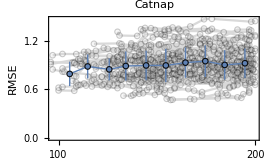

```mathematica
plotData=DeleteCases[resCatnap,{x_,y_}/;x≤95||x>200,{2}];
mean={N@Mean[First/@#],If[Length@#==1,First@#,Around[Mean[#],StandardDeviation[#]]]&[Last/@#]}&/@GatherBy[Sort[Join@@Values@plotData],Floor[First[#],10]&];
mean=Cases[mean,{x_,y_}/;100<x<200];
leg=LineLegend[Directive[Thick,#]&/@{GrayLevel[0.8],ColorData[97][1]},font[#,14]&/@{"Individual Virus","Average Results"},LegendMarkers->plotMarker[0.04,0.8],LegendFunction->frameOpaque,Spacings->{0.2,0.4}];
plotCatnap=Show[ListPlot[plotData,AxesOrigin->{0,0},Frame->{True,True,False,False},PlotLabel->font["Catnap",18],FrameLabel->(font[#,16]&/@{"ΔAA to Nearest Virus","RMSE"}),PlotMarkers->plotMarker[0.025,0.2],PlotRange->{{97,200},{0,1.47}},Joined->True,PlotStyle->LightGray(*,PlotLegends->Placed[leg,Scaled[{{0.33,0.805},{0.5,0.5}}]]*),ImageSize->270,FrameTicks->{LinTicks[0,200,TickLengthScale->2],LinTicks[0,1.6,TickLengthScale->2]},FrameTicksStyle->Directive[16,colorTicks]],ListPlot[mean,PlotMarkers->plotMarker[0.04,0.9],Joined->True,PlotStyle->Thick]]
```

### Figure S7: Using Prior HIV-1 Measurements to Predict Future Measurements

Using existing Catnap measurements up to a certain year to predict either the most potent or the weakest future measurements. More specifically, what number of potent interactions (IC_50<0.1 μg/mL) or weak interactions (IC_50<10 μg/mL) are identified by N experiments (x-axis).

```mathematica
Grid[Table[predictFutureExperiments[year,searchType],{searchType,{"PotentInteractions","WeakInteractions"}},{year,2017,2019}],Spacings->{2,1},ItemSize->All]
```

-Graphics-

## Initialization

### Plot Style

#### Plot Options

```mathematica
Clear[plotMarker,plotMarkerSquare]
plotMarker[size_:0.04,opacity_:1]:={Graphics[{Opacity[opacity],EdgeForm[{Opacity[opacity],Thickness[Tiny],Black}],Disk[{0,0},0.1]}],size};
plotMarkerSquare[size_:0.035,opacity_:1]:={Graphics[{Opacity[opacity],EdgeForm[{Opacity[opacity],Thickness[Tiny],Black}],Rectangle[]}],size};
```

```mathematica
(* Color scheme Dark 2 *)
colors={RGBColor[0.45860547189052764, 0.43899629833399423, 0.7019601145242871],RGBColor[0.4001493096820993, 0.40014898705838536, 0.40014881754595555],RGBColor[0.10735368575582693, 0.6201801935350626, 0.4673715774466202],RGBColor[0.39977958986633894, 0.6510770720392438, 0.11722875093558652],RGBColor[0.6509557752826353, 0.4621627671221546, 0.11250229726888727],RGBColor[0.8513180021016765, 0.3717430799229984, 0.008273519282768628]};
{colorMissing,colorWithheld}={RGBColor[0, 0, 1],RGBColor[1., 0.752940145064468, 2.366108526150601*^-6]};
colorTicks=GrayLevel[0.3];
```

```mathematica
(* To format String expressions *)
font[text_,size_:12,opts___]:=Style[text,FontFamily->"Times",size,opts];
```

```mathematica
(* If Mark Caprio's CustomTicks package can be loaded *)
<<CustomTicks`
SetOptions[LogTicks,LogPlot->True];
```

```mathematica
(* Styling for plot legends *)
Clear[frame,frameOpaque]
frame[leg_,roundingMargin_:0,roundingRadius_:10,frameStyle_:Black]:=Framed[leg,RoundingRadius->roundingRadius,FrameMargins->roundingMargin,FrameStyle->frameStyle,Background->White];
frameOpaque[leg_,roundingMargin_:0,roundingRadius_:10,frameStyle_:Black]:=Framed[leg,RoundingRadius->roundingRadius,FrameMargins->roundingMargin,FrameStyle->frameStyle,Background->Directive[White,Opacity[0.8]]];
```

```mathematica
plotMarker[size_:0.04,opacity_:1]:={Graphics[{Opacity[opacity],EdgeForm[{Opacity[opacity],Thickness[Tiny],Black}],Disk[{0,0},0.1]}],size};
```

#### Swarm Plot

Implementing a Swarm plot

```mathematica
(* https://mathematica.stackexchange.com/questions/42585/implementing-a-beeswarm-plot-in-mathematica *)
intervalInverse[Interval[]]:=Interval[{-∞,∞}]
intervalInverse[Interval[int__]]:=Interval@@Partition[Replace[Flatten@{int},{
{-∞,mid___,∞}:>{mid},
{-∞,mid__}:>{mid,∞},
{mid__,∞}:>{-∞,mid},
{mid___}:>{-∞,mid,∞}
}],2]
intervalComplement[a_Interval,b__Interval]:=IntervalIntersection[a,intervalInverse@IntervalUnion@b]
```

```mathematica
(* 'data' is assumed to be a sorted vector of numbers *)
(* 'radius' specifies the distance between adjacent ponts *)
(* 'xShift' translates all points to the right *)
(* 'xScale' allows for arbitrary aspect ratios *)
swarm[data_,radius_,xShift_:0,xScale_:2]:=Module[{points={},left,right,int},
Do[
int=Interval@@Cases[points,{x_,y_}/;y>pt-radius:>x+xScale/2{-1,1} Sqrt[radius^2-(pt-y)^2]];
right=Min@intervalComplement[Interval[{0,Infinity}],int];
left=Max@intervalComplement[Interval[{-Infinity,0}],int];
AppendTo[points,{If[right<-left,right,left],pt}]
,{pt,data}];
{xShift,0}+#&/@points
]
```

```mathematica
ClearAll[swarmPlot]
Options[swarmPlot]=Join[Options@Graphics,{PlotStyle->Automatic}];
SetOptions[swarmPlot,Frame->True];
SetOptions[swarmPlot,FrameTicks->{None,Automatic}];

swarmPlot[data_?(VectorQ[#,NumericQ]&),radius:(_?NumericQ|Automatic):Automatic,xShift:(_?NumericQ):0,xScale:(_?NumericQ):2,opt:OptionsPattern[]]:=swarmPlot[{data},radius,xShift,xScale,opt]
swarmPlot[data:{__?(VectorQ[#,NumericQ]&)},radius:(_?NumericQ|Automatic):Automatic,xShift:(_?NumericQ):0,xScale:(_?NumericQ):2,opt:OptionsPattern[]]:=Module[{r,order,flatData=Flatten[data],colors,colorFunction},(* Generate color indices and sort them together with the data *)
order=Ordering[flatData];
colors=Flatten@Table[ConstantArray[i,Length@data[[i]]],{i,Length@data}];
flatData=flatData[[order]];
colors=colors[[order]];
(* Automatic radius selection *)
r=If[radius===Automatic,4 Mean@Differences[flatData],2 radius];
(* Handle the PlotStyle option *)
colorFunction=With[{plotStyle=OptionValue[PlotStyle]},
Switch[plotStyle,
Automatic,ColorData[1],
_List,Function[i,plotStyle[[Mod[i,Length@plotStyle,1]]]],
_,plotStyle&
]
];
(* Build graphics using the packing function *)Graphics[MapThread[{colorFunction[#2],Disk[#1,0.95 r/2]}&,{swarm[flatData,r,xShift,xScale],colors}],Sequence@@FilterRules[{opt},Options[Graphics]],Frame->OptionValue[Frame],FrameTicks->OptionValue[FrameTicks]]]
```

```mathematica
(*(* Example data *)
SeedRandom[12345]
data1=RandomVariate[ExponentialDistribution[1],200];
data2=RandomVariate[NormalDistribution[2,1],200];
(* Plot 1 or 2 daasets *)
plot1=swarmPlot[data1];
plot2=swarmPlot[{data1,data2}];
(* Change the color while keeping the radius selection automatic *)
apricot=RGBColor[1.,0.340007,0.129994];
cornflower=RGBColor[0.392193,0.584307,0.929395];
plot3=swarmPlot[{data1,data2},Automatic,PlotStyle->{apricot,cornflower}];
(* Specify the circle radius explicitly in plot coordinates *)
plot4=swarmPlot[data2,0.2];
Grid[{{plot1,plot2,plot3,plot4}},Spacings->3]*)
```

### Importing Data

Influenza data comes from the supplementary information files of Fonville 2014. HIV-1 data comes from Catnap (select the Assay link).

#### Influenza: Antibody-Virus Measurements

Importing the  raw measurements from Fonville 2014 into the variable data:

Table S1: This is the transpose of the original Fonville Table S1, so that the first column represents sera and the first row represents viruses. All other tables were already ordered in this format, so their un-transposed versions are imported.

Some viruses with the same name are labeled with underscores in Table S1 but forward slashes in the other tables, and we unify their names upon import ("HN196_2009"→"HN196/2009"). We also unified names that used short virus names in some tables but long virus names in other tables ("JO/33/94"→"A/JOHANNESBURG/33/94").

Tables S5-S6, S13-S14: The pre-vaccination and post-vaccination sera are distinguished by either having "_Pre" or "_Post" at the end of the serum name

All sera have their Table designation (either S1, S3, S5, S6, S13, or S14) in their name as "_TableX"

```mathematica
(* List of all Fonville supplementary tables *)
fonvilleTables={"S1","S3","S5","S6","S13","S14"};
```

```mathematica
Block[{rawData,table},
MapIndexed[(
rawData=#;
table=fonvilleTables[[First@#2]];
sera[table]=rawData[[2;;,1]];
viruses[table]=rawData[[1,2;;]];
(* Import values in the form: data[{virus,antibody}] *)
Do[
data[{rawData[[1,indexVirus]],rawData[[indexAb,1]]}]=rawData[[indexAb,indexVirus]]
,{indexAb,2,First@Dimensions@rawData},{indexVirus,2,Last@Dimensions@rawData}]
)&
,]
];
```

Each table was individually matrix completed (intra-table completion), and the resulting completions are stored in dataComplete.

```mathematica
(*(* Example: Intra-table completing Table S1 *)
RPCA[Table[N@data[{virus,serum}],{serum,sera["S1"]},{virus,viruses["S1"]}],"LogData"->True]*)
```

```mathematica
Block[{rawData},
MapIndexed[(
rawData=#;
(* Import values in the form: dataComplete[{virus,antibody}] *)
Do[
dataComplete[{rawData[[1,indexVirus]],rawData[[indexAb,1]]}]=rawData[[indexAb,indexVirus]]
,{indexAb,2,First@Dimensions@rawData},{indexVirus,2,Last@Dimensions@rawData}]
)&
,]
];
```

Creating a cumulative list of viruses and sera in Fonville, and then creating the combined dataset containing all six tables. The resulting matrix is (inter-table) matrix completed in the variable dataAllComplete where every virus-serum pair is imputed.

```mathematica
(* Combined viruses and sera in all Fonville tables *)
sera[All]=Join@@sera/@fonvilleTables;
viruses[All]=Sort@DeleteDuplicates[Join@@viruses/@fonvilleTables];
(* Slight aesthetic reordering *)
viruses[All]=ReplacePart[viruses[All],
{21->viruses[All][[22]],
22->viruses[All][[21]],
41->viruses[All][[42]],
42->viruses[All][[41]]
}
];
```

```mathematica
(*(* Example: Inter-table completing all Fonville tables *)
RPCA[Table[N@data[{virus,serum}],{serum,sera[All]},{virus,viruses[All]}],200,"LogData"->True]*)
```

```mathematica
Block[{rawData},
rawData=;
(* Import values in the form: dataAllComplete[{virus,antibody}] *)
Do[
dataAllComplete[{rawData[[1,indexVirus]],rawData[[indexAb,1]]}]=rawData[[indexAb,indexVirus]]
,{indexAb,2,First@Dimensions@rawData},{indexVirus,2,Last@Dimensions@rawData}]
];
```

#### Influenza: Virus Sequences

```mathematica
sequencesFonville=;
```

#### HIV-1: Antibody-Virus Measurements

Importing the raw measurements from Catnap into the variable data:

```mathematica
Block[{rawData,table="Catnap"},
rawData=;
sera[table]=rawData[[2;;,1]];
viruses[table]=rawData[[1,2;;]];
(* Import values in the form: data[{virus,antibody}] *)
Do[
data[{rawData[[1,indexVirus]],rawData[[indexAb,1]]}]=rawData[[indexAb,indexVirus]]
,{indexAb,2,First@Dimensions@rawData},{indexVirus,2,Last@Dimensions@rawData}]
];
```

```mathematica
Block[{rawData,table="CatnapPolyclonal"},
rawData=;
sera[table]=rawData[[2;;,1]];
viruses[table]=rawData[[1,2;;]];
(* Import values in the form: data[{virus,antibody}] *)
Do[
data[{rawData[[1,indexVirus]],rawData[[indexAb,1]]}]=rawData[[indexAb,indexVirus]]
,{indexAb,2,First@Dimensions@rawData},{indexVirus,2,Last@Dimensions@rawData}]
];
```

Each table was matrix completed (intra-table completion), and the resulting completions are stored in dataComplete.

```mathematica
(*(* Example: Intra-table completing the Monoclonal Antibody Dataset *)
(* Note that the Subscript[IC, 50] data is inverted (with the option "InvertData"->True) so that the most potent antibody interactions are represented by the largest values *)
RPCA[Table[N@data[{virus,serum}],{serum,sera["Catnap"]},{virus,viruses["Catnap"]}],200,"LogData"->True,"InvertData"->True]*)
```

```mathematica
Block[{rawData,table="Catnap"},
rawData=;
sera[table]=rawData[[2;;,1]];
viruses[table]=rawData[[1,2;;]];
(* Import values in the form: data[{virus,antibody}] *)
Do[
dataComplete[{rawData[[1,indexVirus]],rawData[[indexAb,1]]}]=rawData[[indexAb,indexVirus]]
,{indexAb,2,First@Dimensions@rawData},{indexVirus,2,Last@Dimensions@rawData}]
];
```

```mathematica
(*(* Example: Intra-table completing the Polyclonal Serum Dataset *)
RPCA[Table[N@data[{virus,serum}],{serum,sera["CatnapPolyclonal"]},{virus,viruses["CatnapPolyclonal"]}],"LogData"->True]*)
```

```mathematica
Block[{rawData,table="CatnapPolyclonal"},
rawData=;
sera[table]=rawData[[2;;,1]];
viruses[table]=rawData[[1,2;;]];
(* Import values in the form: data[{virus,antibody}] *)
Do[
dataComplete[{rawData[[1,indexVirus]],rawData[[indexAb,1]]}]=rawData[[indexAb,indexVirus]]
,{indexAb,2,First@Dimensions@rawData},{indexVirus,2,Last@Dimensions@rawData}]
];
```

#### HIV-1: Virus Sequences

```mathematica
sequencesCatnap=;
```

#### HIV-1: Year of Measurements

```mathematica
yearCatnapMeasurementAbVirus=;
```

```mathematica
(* Year of measurements for each individual antibody or virus *)
yearCatnapMeasurementAb={#[[1,1]],Union[DeleteMissing@Flatten@#[[All,2]]]}&/@GatherBy[yearCatnapMeasurementAbVirus[[All,{1,3}]],First];
yearCatnapMeasurementVirus={#[[1,1]],Union[DeleteMissing@Flatten@#[[All,2]]]}&/@GatherBy[yearCatnapMeasurementAbVirus[[All,{2,3}]],First];
```

#### Helper Functions

```mathematica
(* Which tables each Fonville virus is contained within. Example: containingTables[First@viruses[All]] *)
containingTables[virus_]:=Cases[fonvilleTables,table_/;MemberQ[viruses[table],virus]]
```

```mathematica
(* Fraction of variance explained via Pearson's correlation coefficient squared *)
Clear[correlation]
correlation[data_/;MatchQ[Min[StandardDeviation/@Transpose@data],0|0.]]:=Missing[]
correlation[data_]:=(Correlation@@Transpose@data)^2
```

```mathematica
(* Coefficient of determination R^2 *)
rSquared[data_]:=Module[{mean=Mean[data[[All,2]]]},
1-Total[(#[[1]]-#[[2]])^2&/@data]/Total[(#[[2]]-mean)^2&/@data]
]
```

```mathematica
(* Imported matrix-completed results for inter-table completion and extract the predictions *)
Clear[extractCompletionPredictions]
extractCompletionPredictions[rawImportedData_,{virus_,index:(_String|_List)},data_:None,scaleRowsColsQ_:False]:=Module[{resCompletion,seraIndex,importedData=rawImportedData,scalingRows,scalingCols,headerLeft,headerTop},
If[scaleRowsColsQ,
scalingRows=Prepend[ToExpression@Last@StringSplit[#,", "]&/@importedData[[2;;,1]],1];
scalingCols=Prepend[ToExpression@Last@StringSplit[#,", "]&/@importedData[[1,2;;]],1];
headerLeft=First@StringSplit[#,", "]&/@importedData[[2;;,1]];
headerTop=First@StringSplit[#,", "]&/@importedData[[1]];
importedData=scalingCols #&/@(scalingRows importedData);
importedData=10^importedData;
importedData[[2;;,1]]=headerLeft;
importedData[[1]]=headerTop;
];
seraIndex=Which[
MatchQ[index,_String],Join@@Position[importedData[[All,1]],Alternatives@@sera[index]],
MatchQ[index,_List],index
];
resCompletion=importedData[[seraIndex,Position[importedData[[1]],virus][[1,1]]]];
If[data===None,
(* Return the extracted completions *)
resCompletion,
(* Return the completions together with the measurements *)
Transpose@{resCompletion,Table[data[{virus,serum}],{serum,importedData[[seraIndex,1]]}]}
]
]
```

```mathematica
(* Determine the year of isolation of a virus *)
(* When multiple strains have the same sequence (and hence their names are concatenated with a ";"), take the max year of circulation over all viruses *)
Clear[virusYear]
virusYear[str_String/;!StringContainsQ[str,";"]]:=Module[{year=StringDelete[Last@StringSplit[str,"/"],"_MDCK"|"_EGG"|"-egg"]},
Which[
StringMatchQ[year,DigitCharacter~~DigitCharacter~~DigitCharacter~~DigitCharacter],ToExpression@year,

StringMatchQ[year,DigitCharacter~~DigitCharacter]&&ToExpression@year<50,
ToExpression@year+2000,

StringMatchQ[year,DigitCharacter~~DigitCharacter]&&50≤ToExpression@year<100,
ToExpression@year+1900,

True,
$Failed
]
]
virusYear[str_String/;StringContainsQ[str,";"]]:=Max[virusYear/@StringSplit[str,";"]]
```

```mathematica
(* Generate pre-completion data set, artifically removing data from the virus-sera specified in 'virusToDropInfo' *)
Clear[generateDataLeaveOneOut]
generateDataLeaveOneOut[virusToDropInfo_,dataType_:All,virusesOfInterest_:Automatic,data_:data,scaleRowsColsQ_:False]:=Block[
{listViruses,listSera,virusToDrop,table,fullData,pos},
Switch[
dataType,
All,
listViruses=viruses[dataType];
listSera=sera[dataType],

_List,
listViruses=If[virusesOfInterest===Automatic,
DeleteDuplicates[Join@@viruses/@dataType],
virusesOfInterest
];
listSera=Join@@sera/@dataType
];
(* Combined data from all Fonville tables *)
fullData=Table[data[{virus,serum}],{serum,listSera},{virus,listViruses}];
(* Artifically hiding measurements in 'table' relating to 'virusToDrop'  *)
(
{virusToDrop,table}=#;
pos={#,First@FirstPosition[listViruses,virusToDrop]}&/@First/@Position[listSera,serum_/;StringContainsQ[serum,"Table"<>table~~EndOfString|"_"],{1},Heads->False];
fullData=ReplacePart[fullData,pos->Missing[]]
)&/@virusToDropInfo;
(* Tidy up the data with headers *)
Transpose@Prepend[Transpose@Prepend[fullData,listViruses],Prepend[listSera,"Subject"]]
]
```

```mathematica
(* Fit based on minimizing the perpendicular distance to the best-fit line *)
fitPerp[fitData_,showLineQ_:True]:=Module[{n=Length@fitData,xAvg=Mean@N@fitData[[All,1]],yAvg=Mean@N@fitData[[All,2]],B,b,a,numerator,denominator},
numerator=(Total[fitData[[All,2]]^2]-n yAvg^2)-(Total[fitData[[All,1]]^2]-n xAvg^2);
denominator=n xAvg yAvg-Total[Times@@@fitData];
If[denominator==0.,Return[$Failed]];
B=1./2 numerator/denominator;
b=-B+Sqrt[B^2+1];
a=yAvg-b xAvg;
If[showLineQ,
(* Return best-fit line *)
a+b x,
(* Return RMSE around best-fit line *)
Sqrt@Mean[(fitData[[All,2]]-(a+b fitData[[All,1]]))^2/(1+b^2)]
]
]
```

Helper functions to predict future measurements in Catnap

```mathematica
Clear[analyzeFutureExperiments]
analyzeFutureExperiments[yearPredictionsStart_]:=analyzeFutureExperiments[yearPredictionsStart]=Block[{potentialMeasurements,potentialAbs,potentialViruses,predictionPairs,predictionAbs,predictionViruses,predictionData,posPredictions,rowFullyMissing,colFullyMissing,minNumMeasurements=5},
(* Antibody-virus measurements carried out after 'yearPredictionsStart' *)
potentialMeasurements=Cases[yearCatnapMeasurementAbVirus,{antibody_,virus_,years_}/;Min@years≥yearPredictionsStart:>{antibody,virus}];
(* Antibodies and viruses measured individually before 'yearPredictionsStart' *)
potentialAbs=Cases[yearCatnapMeasurementAb,{antibody_,years_}/;Min@years<yearPredictionsStart:>antibody];
potentialViruses=Cases[yearCatnapMeasurementVirus,{virus_,years_}/;Min@years<yearPredictionsStart:>virus];
(* Restrict to measurements that could be inferred via matrix completion *)
predictionPairs=Cases[potentialMeasurements,{antibody_,virus_}/;MemberQ[potentialAbs,antibody]&&MemberQ[potentialViruses,virus]];
(* Setup the antibody-virus matrix with all potential measurements *)
predictionAbs=Union@predictionPairs[[All,1]];
predictionViruses=Union@predictionPairs[[All,2]];
predictionData=Transpose@Prepend[Transpose@Prepend[Table[data[{virus,antibody}],{antibody,predictionAbs},{virus,predictionViruses}],predictionViruses],Prepend[predictionAbs,"Antibody"]]/.Missing[]->Missing["Not Measured"];
(* After the Ab-virus pairs to be predicted are removed, ensure there are more than 'minNumMeasurements' in each row/column *)
posPredictions=predictionPairs/.Join[Thread[predictionAbs->Range[2,Length@predictionAbs+1]],Thread[predictionViruses->Range[2,Length@predictionViruses+1]]];
predictionData=ReplacePart[predictionData,posPredictions->Missing["Withheld"]];
rowFullyMissing=Position[Length/@DeleteMissing/@predictionData,entry_/;entry≤minNumMeasurements]-1;
colFullyMissing=Position[Length/@DeleteMissing/@Transpose@predictionData,entry_/;entry≤minNumMeasurements]-1;
(* Update the Ab-virus data accordingly *)
predictionAbs=Delete[predictionAbs,rowFullyMissing];
predictionViruses=Delete[predictionViruses,colFullyMissing];
predictionPairs=Cases[potentialMeasurements,{antibody_,virus_}/;MemberQ[potentialAbs,antibody]&&MemberQ[potentialViruses,virus]];
(* This time do not shift the pos indices since we will not append the virus/Ab headers *)
posPredictions=DeleteCases[predictionPairs/.Join[Thread[predictionAbs->Range@Length@predictionAbs],Thread[predictionViruses->Range@Length@predictionViruses]],Except[{_Integer,_Integer}]];
matrixMeasured=Table[data[{virus,antibody}],{antibody,predictionAbs},{virus,predictionViruses}]/.{val_Real:>Log10@val,Missing[]->Missing["Not Measured"]};
{posPredictions,matrixMeasured,RPCA[ReplacePart[matrixMeasured,posPredictions->Missing["Withheld"]]]}
]
```

```mathematica
Clear[predictFutureExperiments]
predictFutureExperiments[
yearPredictionsStart_,
(* Whether to search for potent or weak interactions *)
searchType:"PotentInteractions"|"WeakInteractions"
]:=Block[{matrixMeasured,matrixCompleted,matrixCompletePredictions,numKeyInteractions,slope,plotData,extraLines},
(* {Prediction from matrix completion, measured value} *)
{posPredictions,matrixMeasured,matrixCompleted}=analyzeFutureExperiments[yearPredictionsStart];
matrixCompletePredictions=If[searchType==="PotentInteractions",SortBy,ReverseSortBy][Transpose@{Extract[matrixCompleted,posPredictions],Extract[matrixMeasured,posPredictions]},First];
(* Number of titers matching the criteria *)
numKeyInteractions=Length@Cases[matrixCompletePredictions,{predicted_,measured_}/;If[searchType==="PotentInteractions",measured≤-1.,measured≥1.]];
slope=numKeyInteractions/Length@matrixCompletePredictions;
plotData=Prepend[Transpose@{Range@Length@matrixCompletePredictions,Accumulate[Boole[If[searchType==="PotentInteractions",#[[2]]≤-1.,#[[2]]≥1.]]&/@matrixCompletePredictions]},{0,0}];
(* Demark when 80% of the key interactions are found *)
extraLines=FirstCase[plotData,{measurementsTot_,measurementsKey_}/;measurementsKey≥# numKeyInteractions]&/@{0.8};
(* Plotting *)
Show[ListPlot[plotData,],Plot[{slope x},{x,0,Length@matrixCompletePredictions},],Plot[{x},{x,0,0.85extraLines[[1,-1]]},]]
]
```

### Matrix Completion

#### Robust PCA

This algorithm produces a complete, low-rank matrix using a method that is far faster than nuclear norm minimization, but yields nearly identical results. The algorithm is based on the Candes 2009 manuscript.

This algorithm solves the following problem for a matrix M:

Minimize | (||L||)_*+λ (||S||)_1
Subject to | L+S=M

The key change to this algorithm was to: (1) force the low-rank approximating matrix L to exactly equal the measured values and (2) set λ=0

Larger values of μ tend to yield better results (up to a point), but require more iterations to converge. The default value is μ=0.7

A termination condition checks the similarity between successive L matrices, which works well for the Fonville matrices. If needed, a strict cutoff can be imposed using the numIterations parameter

For the antibody-virus data, mean-centering by subtracting the Min (default option) performs the best

```mathematica
Clear[RPCAShrink,RPCAThreshold];
RPCAShrink[matrix_,0]:=matrix;
RPCAShrink[matrix_,τ_]:=Sign[matrix]*Ramp[Abs[matrix]-τ];
RPCAThreshold[matrix_,τ_,rank_]:=Block[{U,Σ,V},
{U,Σ,V}=SingularValueDecomposition[matrix,rank];
U.RPCAShrink[Σ,τ].Transpose[V]
];
```

```mathematica
(* https://github.com/dganguli/robust-pca *)
(* See Algorithm 1 in: https://arxiv.org/pdf/0912.3599.pdf *)
(* Parameter λ has been fixed to 0, simplifying the algorithm *)
ClearAll[RPCA];
RPCA::usage="RPCA[matrix, iterations, tolerance, μ] performs Robust PCA decomposition of matrix, returning the low rank matrix L";
Options[RPCA]={"ShiftType"->Min,"LogData"->False,"InvertData"->False,"Rank"->Full,"ShowIntermediateIterations"->None};
RPCA[matrixRaw_?MatrixQ,numIterations_Integer:2000,tolerance_Real:10^-6.,μ_Real:0.7,options:OptionsPattern[]]:=Catch[
Block[{rank=OptionValue["Rank"],μInv=1.0/μ,count=0,error=∞,shift,L,Lnew,posMissing,posMeasured,originalMeasured,matrix,blank,reapLists},
matrix=N@matrixRaw/._data|_dataComplete->Missing[];
posMissing=Position[matrix,_Missing,{2},Heads->False];
posMeasured=Position[matrix,Except[_Missing],{2},Heads->False];
(* Whether to transform values into Log10 before completing *)
matrix=matrix/.Which[
TrueQ@OptionValue["LogData"],{val_Real:>If[TrueQ@OptionValue["InvertData"],-1,1]Log10@val},
TrueQ@OptionValue["InvertData"],{val_Real:>1/val},
True,{}
];
(* Whether to use the full matrix rank or decreased rank *)
rank=Which[
rank===Full,Min@Dimensions@matrix,
MatchQ[rank,rank_Integer/;0<rank≤Min@Dimensions@matrix],rank,
True,Throw[$Failed]
];
(* Whether to center the matrix by min-/mean-subtracting *)
shift=Switch[OptionValue["ShiftType"],
Min|Mean,OptionValue["ShiftType"]@DeleteMissing@Flatten@matrix,
None,0.
];
matrix=ReplacePart[matrix-shift,posMissing->0.];
(* Constrain matrix to exactly match the measured values *)
originalMeasured=Thread[posMeasured->Extract[matrix,posMeasured]];
(* Robust PCA Algorithm *)
L=matrix;
Llist=Last@Reap[
While[count<numIterations&&error>tolerance,
Lnew=RPCAThreshold[L,μInv,rank];
error=RootMeanSquare@Extract[L-Lnew,posMissing];
(* Measured values are unchanged *)
L=ReplacePart[Lnew,originalMeasured];
If[MatchQ[OptionValue["ShowIntermediateIterations"],_Integer]&&Divisible[count,OptionValue["ShowIntermediateIterations"]],Sow[{count+1,L+shift},"L"]];
count++
],"L"];
Llist=Join@@Llist;
(* Return the low-rank approximation of the matrix *)
Which[
TrueQ@OptionValue["LogData"],
Llist[[All,-1]]=10^(If[TrueQ@OptionValue["InvertData"],-1,1]Llist[[All,-1]]);
10^(If[TrueQ@OptionValue["InvertData"],-1,1](L+shift)),

TrueQ@OptionValue["InvertData"],
Llist[[All,-1]]=1/Llist[[All,-1]];
1/(L+shift),

True,L+shift
]
]
];
```

```mathematica
(*(* === Example usage === *)
(* Prepare Fonville Table S1 with 70% observed fraction. Values are given as Subscript[log, 10][titer] *)
{Xcomplete,Xincomplete}=prepareIntraTableCompletion["S1",0.7];
posWithheld=Position[Xincomplete,Missing["Withheld"]];
(* Perform robust PCA and compute the RMSE error of the withheld values *)
res=RPCA[Xincomplete,"ShowIntermediateIterations"->10];
Echo[RootMeanSquare[Subtract@@@Transpose@{Extract[res,posWithheld],Extract[Xcomplete,posWithheld]}],"RMSE for withheld values:"];
(* Plot the prediction error as a function of the # of iterations [blue] as well as the RMSE between successive iterations [gold] *)
ListPlot[{Transpose@{First/@Llist,RootMeanSquare[Subtract@@@Transpose@{Extract[#,posWithheld],Extract[Xcomplete,posWithheld]}]&/@Last/@Llist},Transpose@{Rest[First/@Llist],RootMeanSquare@Extract[#[[1]]-#[[2]],posWithheld]&/@Partition[Last/@Llist,2,1]}},PlotRange->{10^-6,10^0.4},Joined->True,PlotMarkers->Automatic,ScalingFunctions->"Log",Frame->{True,True,False,False},FrameLabel->(font[#,14]&/@{"Iteration","RMSE (log_10 titers)"}),FrameTicks->{LinTicks[300,0,TickLengthScale->2],LogTicks[10^-6,10^1,TickLengthScale->2]},PlotLegends->PointLegend[font[#,14]&/@{"Prediction Error","Successive Deviations"},LegendFunction->"Frame"]]*)
```

#### Nuclear Norm Minimization

The classical approach to matrix completion by minimizing the nuclear norm. This algorithm works well, but it scales poorly with the size of the matrix.

```mathematica
Clear[symmetricMatrix]
symmetricMatrix[var_,size_]:=Normal@SymmetrizedArray[{j_,k_}:>Indexed[var,{j,k}],{size,size},Symmetric[{1,2}]]
```

```mathematica
ClearAll[nuclearNormMinimization]
Options[nuclearNormMinimization]={"ShiftType"->Min,"LogData"->False,"InvertData"->False};
nuclearNormMinimization[matrixRaw_?MatrixQ,options:OptionsPattern[]]:=Block[{shift,matrix,x,posMissing,n,m,U,V,mat,u,v},
(* Whether to transform values into Log10 before completing *)
matrix=N@matrixRaw/.Which[
TrueQ@OptionValue["LogData"],{val_Real:>If[TrueQ@OptionValue["InvertData"],-1,1]Log10@val},
TrueQ@OptionValue["InvertData"],{val_Real:>1/val},
True,{}
];
(* Whether to center the matrix by min-/mean-subtracting *)
shift=Switch[OptionValue["ShiftType"],
Min|Mean,OptionValue["ShiftType"]@DeleteMissing@Flatten@matrix,
None,0.
];
matrix=matrix-shift;
(* Change all Missing elements to Indexed elements that can be solved numerically *)
matrix=ReplacePart[matrix,#->Indexed[x,#]&/@Position[matrixRaw,_Missing]];
(* Set up SemidefiniteOptimization *)
{n,m}=Dimensions@matrix;
U=symmetricMatrix[u,n];
V=symmetricMatrix[v,m];
mat=Transpose@Join[Transpose@Join[U,Transpose[matrix]],Transpose@Join[matrix,V]];
(* Complete the missing entries *)
Which[
TrueQ@OptionValue["LogData"],10^(If[TrueQ@OptionValue["InvertData"],-1,1](matrix+shift)),
TrueQ@OptionValue["InvertData"],1/(matrix+shift),
True,matrix+shift
]/.SemidefiniteOptimization[Tr[U]+Tr[V],mat(\[VectorGreaterEqual])_("SemidefiniteCone")0,Variables@{matrix,U,V},Method->"SCS"]
]
```

```mathematica
(* Nuclear norm of a matrix *)
nuclearNorm[mat_]:=Total@SingularValueList@mat
(* Nuclear norm (alternate, slower formulation) *)
(*nuclearNorm[mat_]:=Tr[MatrixPower[ConjugateTranspose[mat].mat,1./2]]*)
```

Example completion

```mathematica
(*pos={{1,2},{3,4},{5,1},{2,4}};
X=# Range@5&/@ Range@5;
(X[[Sequence@@#]]=Missing[])&/@pos;
(X//MatrixForm)->(nuclearNormMinimization[X]//MatrixForm)//Timing*)
```